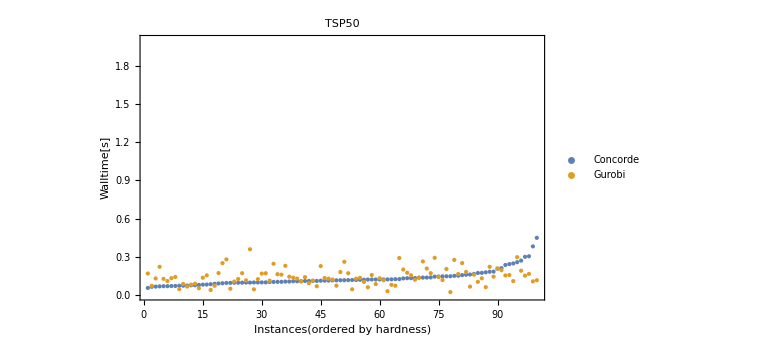

```mathematica
concorde=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/concorde/50n_0423-1647.csv", Numeric->True];
gurobi=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/gurobi/50n_0423-2109.csv", Numeric->True];
concorde=Delete[concorde,1];
gurobi=Delete[gurobi,1];
concorde=Part[#,2]&/@concorde;
gurobi=Part[#,2]&/@gurobi;
{concorde,gurobi}=SortBy[{concorde,gurobi}ᵀ,First]ᵀ;
plot=Show[
ListPlot[{concorde,gurobi},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"Concorde","Gurobi"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[concorde,gurobi]],0],Ceiling[Max[concorde,gurobi]]+1}},
PlotLabel->Style["TSP50"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/Concorde_vs_Gurobi/tsp50.png",plot];
```

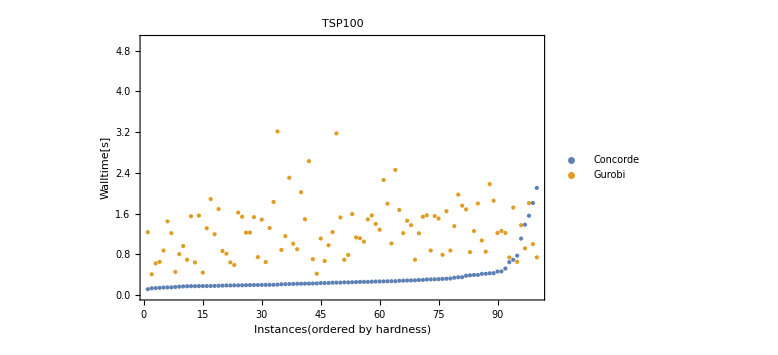

```mathematica
concorde=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/concorde/100n_0423-1653.csv", Numeric->True];
gurobi=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/gurobi/100n_0423-2109.csv", Numeric->True];
concorde=Delete[concorde,1];
gurobi=Delete[gurobi,1];
concorde=Part[#,2]&/@concorde;
gurobi=Part[#,2]&/@gurobi;
{concorde,gurobi}=SortBy[{concorde,gurobi}ᵀ,First]ᵀ;
plot=Show[
ListPlot[{concorde,gurobi},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"Concorde","Gurobi"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[concorde,gurobi]],0],Ceiling[Max[concorde,gurobi]]+1}},
PlotLabel->Style["TSP100"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/Concorde_vs_Gurobi/tsp100.png",plot];
```